8

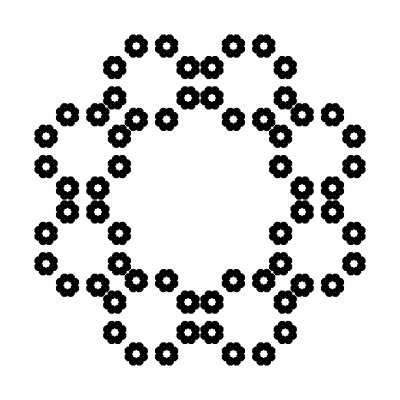

-Graphics-

```mathematica
nPoints = 8

createCirclyCoords[{point_, scale_}] := Table[point + x*scale,{x,CirclePoints[nPoints]}]

Graphics[
Point[
FlattenAt[
Table[createCirclyCoords[{z,.015}], {z, 
FlattenAt[
Table[createCirclyCoords[{y,.05}], {y, 
FlattenAt[
Table[createCirclyCoords[{x, .25}], {x, CirclePoints[nPoints]*.8}],
Table[{a},{a, 1, nPoints^1, 1}]
]
}],
Table[{b},{b,1,nPoints^2,1}]
]}
],
Table[{c},{c,1,nPoints^3,1}]
]
],
ImageSize->Full
]

Graphics[
Point[
FlattenAt[
Table[createCirclyCoords[{y,.05}], {y, 
FlattenAt[
Table[createCirclyCoords[{x, .25}], {x, CirclePoints[6]}],
Table[{a},{a, 1, 6, 1}]
]
}],
Table[{b},{b,1,36,1}]
]
]
]
```